# Amplitud final

## Max coefficient value in the final time with different noises.

We need to import the files “cT3a.txt”,”cT5a.txt” and “cT7a.txt”.  This files where generated in the “fourier coefficient for Fig 5” notebook. This files can be find the  same folder.

## Data importation

### Data Import: (*change it to the local directory where the “cT3a.txt”,”cT5a.txt” and “cT7a.txt” files are*)

```mathematica
directorio="(*your directory here*)\\";
```

### Data importation

We need to remember that :

 b=1.76921 for  n3
 b=1.82272 for n5 and 
 b=1.903 for n7

```mathematica
n3=Import[StringJoin[directorio,"cT3a.txt"],"TSV"];
n5=Import[StringJoin[directorio,"cT5a.txt"],"TSV"];
```

```mathematica
n7=Import[StringJoin[directorio,"cT7a.txt"],"TSV"];
```

```mathematica
n3=ToExpression[n3];
n5=ToExpression[n5];
n7=ToExpression[n7];
```

## Tables of values

Now with the imported data we look for the maximum value for each row of our matrix, that is, for the different n.b4s

```mathematica
(*max value position tables*)
mx3(*noise,n*)=Table[Position[n3⟦n,t⟧,Max[Abs[ToExpression[n3⟦n,t⟧⟦2;;⟧]]]]⟦1,1⟧,{n,1,Dimensions[n3]⟦1⟧},{t,1,Dimensions[n3]⟦2⟧}]+9;
```

```mathematica
mx5=Table[Position[n5⟦n,t⟧,Max[Abs[ToExpression[n5⟦n,t⟧]]]]⟦1,1⟧,{n,1,Dimensions[n5]⟦1⟧},{t,1,Dimensions[n5]⟦2⟧}]+9;
```

```mathematica
mx7=Table[Position[n7⟦n,t⟧,Max[Abs[ToExpression[n7⟦n,t⟧⟦2;;⟧]]]]⟦1,1⟧,{n,1,Dimensions[n7]⟦1⟧},{t,1,Dimensions[n7]⟦2⟧}]+9;
```

```mathematica
mx3(*noise,n*)//Transpose//MatrixForm
```

(12 | 15 | 14 | 15 | 16 | 17 | 12
15 | 14 | 14 | 15 | 16 | 15 | 15
15 | 14 | 14 | 15 | 16 | 15 | 15
15 | 14 | 14 | 15 | 16 | 15 | 15
15 | 14 | 14 | 15 | 16 | 15 | 15
15 | 14 | 14 | 15 | 16 | 15 | 15
15 | 14 | 14 | 15 | 16 | 15 | 15
14 | 14 | 14 | 15 | 16 | 15 | 14
15 | 15 | 14 | 15 | 16 | 15 | 15
15 | 14 | 14 | 15 | 16 | 15 | 15
16 | 14 | 14 | 15 | 16 | 15 | 15
15 | 15 | 14 | 15 | 16 | 15 | 15
15 | 15 | 14 | 15 | 16 | 15 | 15
15 | 15 | 14 | 15 | 16 | 15 | 15
15 | 14 | 14 | 15 | 16 | 15 | 15
15 | 14 | 14 | 15 | 16 | 15 | 15
15 | 15 | 14 | 15 | 16 | 15 | 15
15 | 15 | 14 | 15 | 16 | 15 | 15
15 | 15 | 14 | 15 | 16 | 15 | 15
15 | 15 | 14 | 15 | 16 | 15 | 15
15 | 15 | 15 | 15 | 16 | 15 | 15
15 | 15 | 14 | 15 | 16 | 15 | 15
15 | 14 | 14 | 15 | 16 | 15 | 14
15 | 15 | 14 | 15 | 15 | 15 | 15
15 | 15 | 14 | 15 | 15 | 15 | 15
16 | 16 | 15 | 15 | 15 | 16 | 16
15 | 15 | 14 | 15 | 15 | 15 | 15
15 | 15 | 14 | 15 | 16 | 15 | 15
15 | 15 | 14 | 15 | 15 | 15 | 15
15 | 15 | 14 | 15 | 15 | 15 | 15
14 | 15 | 15 | 15 | 14 | 14 | 14
14 | 15 | 14 | 15 | 15 | 15 | 15
14 | 14 | 15 | 15 | 15 | 14 | 14
15 | 14 | 15 | 15 | 15 | 15 | 15
15 | 15 | 14 | 15 | 16 | 15 | 15
15 | 15 | 15 | 15 | 15 | 15 | 15
15 | 14 | 14 | 15 | 14 | 14 | 15
15 | 16 | 15 | 15 | 15 | 15 | 15
15 | 15 | 15 | 15 | 15 | 15 | 15
15 | 15 | 15 | 15 | 15 | 15 | 15
15 | 15 | 15 | 15 | 14 | 15 | 15
15 | 15 | 15 | 15 | 15 | 15 | 15)

```mathematica
mx5(*noise,n*)//Transpose//MatrixForm
```

(14 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 14
15 | 12 | 13 | 14 | 15 | 16 | 17 | 15 | 15
15 | 12 | 13 | 14 | 15 | 16 | 17 | 15 | 15
16 | 12 | 13 | 14 | 15 | 16 | 17 | 14 | 14
15 | 14 | 13 | 14 | 15 | 16 | 17 | 14 | 15
15 | 14 | 13 | 14 | 15 | 16 | 17 | 15 | 15
15 | 12 | 13 | 14 | 15 | 16 | 17 | 15 | 15
15 | 13 | 13 | 14 | 15 | 16 | 17 | 15 | 14
16 | 14 | 13 | 14 | 15 | 16 | 16 | 15 | 16
15 | 14 | 13 | 14 | 15 | 16 | 17 | 15 | 14
15 | 15 | 13 | 14 | 15 | 16 | 15 | 15 | 15
14 | 14 | 13 | 14 | 15 | 16 | 17 | 15 | 14
15 | 14 | 13 | 14 | 15 | 16 | 16 | 15 | 14
15 | 14 | 13 | 14 | 15 | 16 | 15 | 15 | 14
15 | 15 | 13 | 14 | 15 | 16 | 16 | 15 | 15
15 | 15 | 13 | 14 | 15 | 16 | 14 | 14 | 14
14 | 13 | 13 | 14 | 15 | 16 | 16 | 15 | 14
15 | 15 | 14 | 14 | 15 | 16 | 15 | 15 | 15
15 | 15 | 14 | 14 | 15 | 16 | 15 | 15 | 15
14 | 15 | 13 | 14 | 15 | 16 | 15 | 14 | 14
15 | 14 | 14 | 14 | 15 | 15 | 16 | 15 | 14
15 | 15 | 14 | 14 | 15 | 15 | 15 | 15 | 15
15 | 15 | 15 | 15 | 15 | 16 | 16 | 15 | 15
15 | 15 | 15 | 14 | 15 | 15 | 15 | 15 | 15
15 | 15 | 15 | 15 | 15 | 16 | 15 | 15 | 14
15 | 15 | 15 | 14 | 15 | 15 | 15 | 14 | 15
15 | 15 | 14 | 14 | 15 | 15 | 15 | 15 | 15
14 | 14 | 14 | 15 | 15 | 14 | 14 | 14 | 14
14 | 14 | 14 | 14 | 15 | 15 | 15 | 15 | 15
15 | 15 | 14 | 15 | 14 | 15 | 14 | 14 | 15
15 | 15 | 15 | 14 | 15 | 16 | 15 | 15 | 15
14 | 14 | 13 | 14 | 15 | 16 | 15 | 15 | 15
14 | 14 | 13 | 15 | 15 | 14 | 14 | 14 | 14
15 | 14 | 14 | 14 | 15 | 14 | 15 | 14 | 15
15 | 15 | 16 | 16 | 15 | 15 | 15 | 15 | 15
15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15
15 | 15 | 14 | 15 | 15 | 16 | 15 | 15 | 15
15 | 14 | 15 | 14 | 15 | 15 | 15 | 15 | 15)

```mathematica
mx7(*noise,n*)//Transpose//MatrixForm
```

(12 | 12 | 13 | 14 | 15 | 16 | 17 | 12 | 12
13 | 12 | 13 | 14 | 15 | 16 | 17 | 13 | 14
12 | 12 | 13 | 14 | 15 | 16 | 17 | 14 | 14
12 | 12 | 13 | 14 | 15 | 16 | 17 | 13 | 13
14 | 12 | 13 | 14 | 15 | 16 | 17 | 14 | 13
14 | 12 | 13 | 14 | 15 | 16 | 17 | 15 | 14
12 | 12 | 13 | 14 | 15 | 16 | 17 | 14 | 15
13 | 12 | 13 | 14 | 15 | 16 | 17 | 13 | 14
15 | 12 | 13 | 14 | 15 | 16 | 17 | 15 | 15
13 | 12 | 13 | 14 | 15 | 16 | 17 | 14 | 13
14 | 12 | 13 | 14 | 15 | 16 | 16 | 15 | 14
13 | 12 | 13 | 14 | 15 | 16 | 17 | 13 | 14
13 | 12 | 13 | 14 | 15 | 16 | 17 | 14 | 14
13 | 14 | 13 | 14 | 15 | 16 | 15 | 14 | 14
14 | 13 | 13 | 14 | 15 | 16 | 16 | 14 | 14
14 | 13 | 13 | 14 | 15 | 16 | 15 | 14 | 14
14 | 13 | 13 | 14 | 15 | 16 | 16 | 14 | 13
14 | 15 | 14 | 14 | 15 | 16 | 15 | 14 | 15
15 | 13 | 13 | 14 | 15 | 16 | 15 | 15 | 15
14 | 14 | 13 | 14 | 15 | 14 | 14 | 14 | 14
15 | 12 | 13 | 14 | 15 | 16 | 15 | 15 | 14
15 | 13 | 14 | 14 | 15 | 15 | 14 | 15 | 15
14 | 14 | 15 | 14 | 15 | 14 | 15 | 14 | 15
13 | 13 | 13 | 14 | 15 | 15 | 14 | 13 | 13
14 | 14 | 14 | 14 | 15 | 16 | 16 | 15 | 15
14 | 15 | 15 | 14 | 14 | 15 | 15 | 14 | 15
15 | 13 | 13 | 14 | 14 | 15 | 15 | 14 | 14
14 | 14 | 14 | 15 | 15 | 14 | 14 | 14 | 14
14 | 12 | 13 | 14 | 15 | 14 | 15 | 14 | 13
14 | 14 | 14 | 14 | 14 | 14 | 14 | 14 | 14
14 | 15 | 14 | 15 | 15 | 15 | 15 | 15 | 14
12 | 12 | 13 | 14 | 15 | 14 | 14 | 12 | 13
14 | 15 | 14 | 14 | 15 | 14 | 15 | 14 | 14
14 | 13 | 13 | 14 | 14 | 13 | 13 | 13 | 13
15 | 15 | 15 | 16 | 15 | 15 | 14 | 15 | 15
15 | 15 | 15 | 14 | 15 | 15 | 15 | 15 | 15
14 | 14 | 14 | 13 | 15 | 15 | 14 | 14 | 14
14 | 13 | 13 | 13 | 14 | 13 | 13 | 14 | 13
14 | 14 | 14 | 15 | 15 | 15 | 14 | 15 | 14)

We change the max fourier coefficient for when noise=0 to hace the inicial max fourier coefficient

```mathematica
mx3⟦;;,1⟧={12,13,14,15,16,17,18};
mx5⟦;;,1⟧={11,12,13,14,15,16,17,18,19};
mx7⟦;;,1⟧={11,12,13,14,15,16,17,18,19};
```

We make a list of the noise values

```mathematica
noise3=Join[Table[i,{i,0,.28,.02}],Table[i,{i,.3,1.25,.05}],Table[i,{i,1.3,1.9,.1}]];
noise5=Join[Table[i,{i,0,.275,.025}],Table[i,{i,.3,1.25,.05}],Table[i,{i,1.3,1.8,.1}]];
noise7=Join[Table[i,{i,0,.275,.025}],Table[i,{i,.3,1.25,.05}],Table[i,{i,1.3,1.9,.1}]];
```

We assign noise to our rows

```mathematica
tr3=Table[{mx3⟦j,i⟧,noise3⟦i⟧},{j,1,Length[mx3]},{i,1,Length[noise3]}];
tr5=Table[{mx5⟦j,i⟧,noise5⟦i⟧},{j,1,Length[mx5]},{i,1,Length[noise5]}];
tr7=Table[{mx7⟦j,i⟧,noise7⟦i⟧},{j,1,Length[mx5]},{i,1,Length[noise7]}];
```

## Plots

### Dot plots

```mathematica
tr33=Table[{mx3⟦j,i⟧,noise3⟦i⟧},{j,1,Length[mx3]},{i,1,Length[noise3]}];
tr53=Table[{mx5⟦j,i⟧+0.1,noise5⟦i⟧},{j,1,Length[mx5]},{i,1,Length[noise5]}];
tr73=Table[{mx7⟦j,i⟧-0.1,noise7⟦i⟧},{j,1,Length[mx7]},{i,1,Length[noise7]}];
```

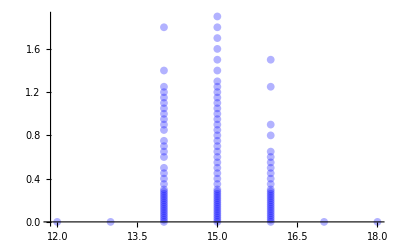

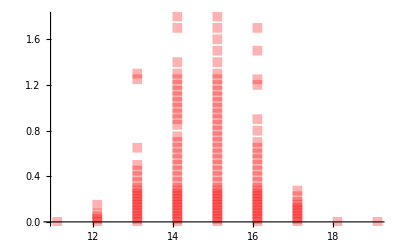

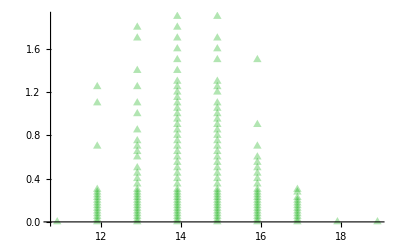

```mathematica
pli3=ListPlot[DeleteDuplicates[Flatten[tr33,1]],PlotStyle->Opacity[0.3,Blue],PlotMarkers->{"●",8}]
pli5=ListPlot[DeleteDuplicates[Flatten[tr53,1]],PlotStyle->Opacity[0.3,Red],PlotMarkers->{"■",10}]
pli7=ListPlot[DeleteDuplicates[Flatten[tr73,1]],PlotStyle->Opacity[0.3,Darker[Green]],PlotMarkers->{"▲",10}]
```

### Final Plot

List of stables max fourier coefficient

```mathematica
plo3=Table[Flatten[Position[mx3[[i-11]],i]],{i,12,18}];
plo5=Table[Flatten[Position[mx5[[i-10]],i]],{i,11,19}];
plo7=Table[Flatten[Position[mx7[[i-10]],i]],{i,11,19}];
```

Position of the last stable max fourier coefficient

```mathematica
pos3={1,2,21,42,23,2,1};
pos5={1,5,18,25,30,21,9,2,1};
pos7={1,14,22,28,26,20,11,1,1};
```

Table of noise vs n

```mathematica
p3=Table[{i+11,noise3⟦pos3⟦i⟧⟧},{i,1,Length[pos3]}];
p5=Table[{i+10,noise5⟦pos5⟦i⟧⟧},{i,1,Length[pos5]}];
p7=Table[{i+10,noise7⟦pos7⟦i⟧⟧},{i,1,Length[pos7]}];
```

Related graphs of noise vs n

```mathematica
la3=ListPlot[p3,Joined->True,InterpolationOrder->2,PlotRange->{-0.1,2.1},AspectRatio->1/1.5, Frame->True, FrameTicks->{{None,{0.5,1.0,1.5}},{None,{11,13,15,17,19}}}, ImageSize->400, FrameTicksStyle->Directive[Gray,24], PlotStyle->{Blue,Thickness[0.0075]},FrameLabel->{Text[Style["n",28,Italic, Black]],Text[Style["noise",28,Italic, Black]]}];
la5=ListPlot[p5,Joined->True,InterpolationOrder->2,PlotRange->{-0.1,1.7},AspectRatio->1/1.5, Frame->True, FrameTicks->{{None,{0,0.5,1.0,1.5,2}},{None,{11,13,15,17,19}}}, ImageSize->400, FrameTicksStyle->Directive[Gray,24],  PlotStyle->{Red,Thickness[0.0075]},FrameLabel->{Text[Style["n",28,Italic, Black]],Text[Style["|ξ(x)|",28,Italic, Black]]}];
la7=ListPlot[p7,Joined->True,InterpolationOrder->2,PlotRange->{-0.1,1.7},AspectRatio->1/1.5, Frame->True, FrameTicks->{{None,{0.5,1.0,1.5}},{None,{11,12,13,14,15,16,17,18,19}}}, ImageSize->400, FrameTicksStyle->Directive[Gray,24],  PlotStyle->{Darker[Green],Thickness[0.0075]},FrameLabel->{Text[Style["n",28,Italic, Black]],Text[Style["noise",28,Italic, Black]]}];
```

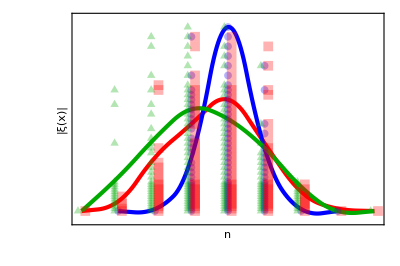

```mathematica
noisef=Show[la5,la3,la7,pli3,pli5,pli7,PlotRange->{-0.1,2.0}]
```

```mathematica
Export["noise.png",noisef,ImageResolution->250]
```

noise.png